Задание
 
По указанному правилу сгенерировать 150 точек (x,y) и добавить к целевой переменной y случайный шум из нормального распределения с указанным отклонением σ. 

100 точек использовать для построения модели.
50 для тестирования и выбора гиперпараметра λ.
 
1. Методом наименьших квадратов на обучающей выборке построить полиномиальную регрессию достаточно высокого порядка (например, 15), визуализировать полученную модель и оценить MSE на отложенной выборке.
2. Построить гребневую регрессию. На отложенной выборке выбрать оптимальный параметр λ.
3. Построить лассо-регрессию. На отложенной выборке выбрать оптимальный параметр λ.
4. Сравнить качество результатов визуально и с помощью MSE.

Указания
 
1. При генерации точек фиксировать SeedRandom.
2. В названии файла указать фамилию и тему работы.

```mathematica
Вариант 13
f(x)=(1-x)·sin(x)·cos(x)
σ=0.1
x∈[-1,3]
```

## 0. Generator

```mathematica
ClearAll[generator,n,σ,x,f]
```

## Parameters

```mathematica
n=150;
σ=0.1;
f[x_]:=Sin[x]*Cos[x]*(1-x)
{xmin,xmax}={-1,3};
```

## Generator Function

```mathematica
Options[generator] = {PlotPoints->n, RandomSeed->1234};
generator[f_,{x_, xmin_, xmax_}, OptionsPattern[]]:=Module[{n = OptionValue[PlotPoints], s = OptionValue[RandomSeed]},
BlockRandom[SeedRandom[s];
Table[{x, f},{x,RandomReal[{xmin, xmax}, n]}]+RandomVariate[NormalDistribution[0,σ],n]]]
```

```mathematica
generate=SortBy[generator[f[x],{x,xmin,xmax}],First];
```

## Visualisation

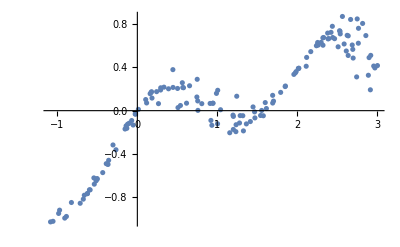

```mathematica
ListPlot[generate]
```

## Train Set

```mathematica
train = generate[[;;100]];
```

## Test Set

```mathematica
test=generate[[101;;]];
```

## 1. Generator

## Train | Test Split

```mathematica
xtrain = train[[All,1]];
ytrain = train[[All,2]];
xtest=test[[All,1]];
ytest=test[[All,2]];
```

## Polynom Function

```mathematica
ClearAll[polynom]
polynom[x_,degree_]:=Sum[Subscript[θ, j]*x^j,{j,0,degree}]
polynom[{Subscript[x, 1]},4]
```

{θ_0+x_1 θ_1+x_1^2 θ_2+x_1^3 θ_3+x_1^4 θ_4}

## Coefficients of Polynom

```mathematica
ClearAll[coefficients]
coefficients[i_]:=Subscript[θ, i]
```

## Points (for ListPlot)

```mathematica
ClearAll[point]
point[x_,y_]:={x,y}
Thread[point[{1,2,3},{4,5,6}]]
```

{{1,4},{2,5},{3,6}}

## Polyfit

```mathematica
polyfit[xtrain_,ytrain_,degree_,typePolynom_]:=Module[{polytrain=typePolynom[xtrain,degree],coefs=Thread[coefficients[Range[0,degree]]],l=Length[xtrain]},
lsm=Total@((polytrain-ytrain)^2);
fitLSM=Minimize[lsm,coefs];

yFit=polytrain/.fitLSM⟦2⟧;
mse = Total[(yFit-ytrain)^2]/l;
pointsYpred=Thread[point[xtrain,yFit]];
{pointsYpred,mse,fitLSM⟦2⟧}]
```

```mathematica
m=1;
{polyTrain,mseTrain,fitParams} = polyfit[xtrain,ytrain,m,polynom];
```

## Visualisation Polyfit

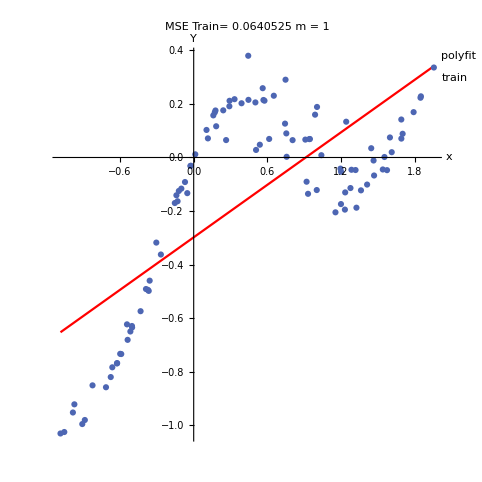

```mathematica
plotLabel="MSE Train= "~~ToString[mseTrain,TraditionalForm]~~"\n m = "~~ToString@m;
ListPlot[{polyTrain,train},
AspectRatio->1,AxesLabel->{"x","Y"},
Joined->{True,False},PlotLabel->plotLabel,
PlotLabels->Placed[{"polyfit","train"},After],
PlotStyle->{Red,RGBColor[0.3,0.4,0.7]}]
```

## Test Polyfit

```mathematica
polytest[xtest_,ytest_,params_,degree_,typePolynom_]:=Module[{polyT=typePolynom[xtest,degree]/.params,l=Length[xtest]},
mseTest = Total[(polyT-ytest)^2]/l;
polyYTest=Thread[point[xtest,polyT]];
{polyYTest,mseTest }]
```

```mathematica
{polyTest,mseTest} = polytest[xtest,ytest,fitParams,m,polynom];
```

## Visualisation Polyfit Test

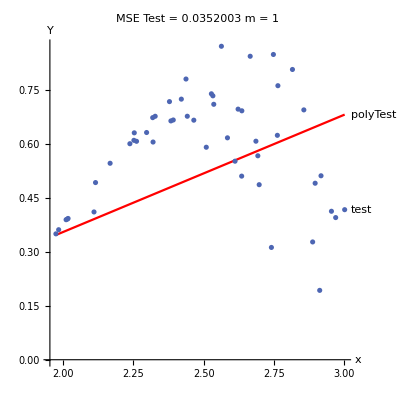

```mathematica
{polyTest,mseTest}=polytest[xtest,ytest,polyfit[xtrain,ytrain,m,polynom]⟦3⟧,m,polynom];
plotLabel="MSE Test = "~~ToString[mseTest,TraditionalForm]~~"\n m = "~~ToString@m;
ListPlot[{polyTest,test},
AspectRatio->1,AxesLabel->{"x","Y"},
Joined->{True,False},PlotLabel->plotLabel,
PlotLabels->Placed[{"polyTest","test"},After],
PlotStyle->{Red,RGBColor[0.3,0.4,0.7]}]
```

## MSE (Degrees)

```mathematica
mseTestSet=Table[polytest[xtest,ytest,polyfit[xtrain,ytrain,i,polynom]⟦3⟧,i,polynom]⟦2⟧,{i,1,15}]
```

{0.0352003,1.56129,0.119625,20.2093,2.46105,28.9379,0.0509167,18.9407,1.17764,2112.75,65769.4,24364.4,641276.,1.6708×10^7,1.45249×10^7}

## Visualisation Polyfit Test (Degrees=15)

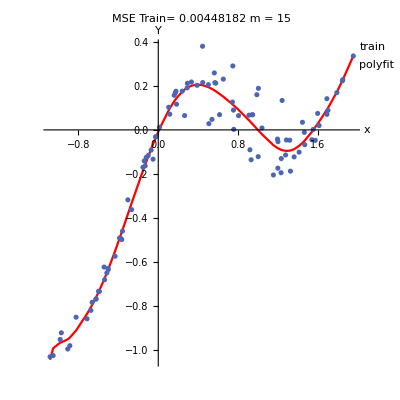

```mathematica
m=15;
{polyTrain,mseTrain,fitParams} = polyfit[xtrain,ytrain,m,polynom];
plotLabel="MSE Train= "~~ToString[mseTrain,TraditionalForm]~~"\n m = "~~ToString@m;
ListPlot[{polyTrain,train},
AspectRatio->1,AxesLabel->{"x","Y"},
Joined->{True,False},PlotLabel->plotLabel,
PlotLabels->Placed[{"polyfit","train"},After],
PlotStyle->{Red,RGBColor[0.3,0.4,0.7]}]
```

О, полином 15-ой степени прекрасно подобрался с минимальной MSE на тренировочных точках. Но что же будет на тестовом множестве?..

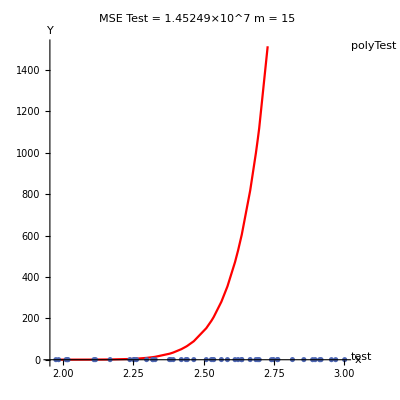

```mathematica
m=15;
{polyTest,mseTest}=polytest[xtest,ytest,polyfit[xtrain,ytrain,m,polynom][[3]],m,polynom];
plotLabel="MSE Test = "~~ToString[mseTest,TraditionalForm]~~"\n m = "~~ToString@m;
ListPlot[{polyTest,test},
AspectRatio->1,AxesLabel->{"x","Y"},
Joined->{True,False},PlotLabel->plotLabel,
PlotLabels->Placed[{"polyTest","test"},After],
PlotStyle->{Red,RGBColor[0.3,0.4,0.7]}]
```

Видим, что модель переобучилась на тренировочных данных. На тестовых данных невероятная MSE ошибка!

## 2. Ridge Regression

## Ridge Regression Function

```mathematica
Clear[λ,ridgePolynom]
polyRidge[xtrain_,ytrain_,degree_,typePolynom_,λ_,step_]:=Module[
{
polytrain=typePolynom[xtrain,degree,λ,step],
coefs=Thread[coefficients[Range[0,degree]]],
l=Length[xtrain]
},
lsm=Total@((polytrain-ytrain)^2);
fitLSM=Minimize[lsm,coefs];
yFit=polytrain/.fitLSM⟦2⟧;
mse = Total[(yFit-ytrain)^2]/l;
pointsYpred=Thread[point[xtrain,yFit]];
{pointsYpred,mse,fitLSM⟦2⟧}]
```

```mathematica
ridgePolynom[x_,degree_,λ_,step_]:=Sum[Subscript[θ, j]*x^j,{j,0,degree}]+λ*∑_(j=0)^degree Abs[Subscript[θ, j]]^step
ridgePolynom[{Subscript[x, 1]},4,0.5,2]
```

{0.5 (Abs[θ_0]^2+Abs[θ_1]^2+Abs[θ_2]^2+Abs[θ_3]^2+Abs[θ_4]^2)+θ_0+x_1 θ_1+x_1^2 θ_2+x_1^3 θ_3+x_1^4 θ_4}

## Ridge Polyfit (step - степень возведения коэффициентов в степень).

```mathematica
m=2;
λ=0.5;
step=2;
{polyTrainRidge,mseTrainRidge,fitParamsRidge} = polyRidge[xtrain,ytrain,m,ridgePolynom,λ,step];
```

```mathematica
fitParamsRidge
```

{θ_0→-0.481068,θ_1→0.591963,θ_2→-0.308634}

## Test Ridge Polyfit

```mathematica
polytestRidge[xtest_,ytest_,params_,degree_,typePolynom_,λ_,step_]:=Module[{polyT=typePolynom[xtest,degree,λ,step]/.params,l=Length[xtest]},
mseTest = Total[(polyT-ytest)^2]/l;
polyYTest=Thread[point[xtest,polyT]];
{polyYTest,mseTest }]
```

```mathematica
{polyTestRidge,mseTestRidge} = polytestRidge[xtest,ytest,fitParamsRidge,m,ridgePolynom,λ,step];
```

## Min (λ,15) Ridge

```mathematica
start=0;
end=30;
stepik=0.05
bestFitLambdaRidge=Table[polytestRidge[xtest,ytest,polyRidge[xtrain,ytrain,15,ridgePolynom,λ,step=2][[3]],15,ridgePolynom,λ,step=2][[2]],{λ,start,end,stepik}];
```

0.05

```mathematica
posMin=Flatten@Position[bestFitLambdaRidge,Min[bestFitLambdaRidge]];
bestLambdaRidge=Range[start,end,stepik]⟦posMin⟧
minMSEridge=bestFitLambdaRidge⟦posMin⟧
```

{23.3}

{804.527}

## Visualisation Polyfit Test Best Result

{θ_0→-0.0214592,θ_1→0.0169889,θ_2→-0.0125931,θ_3→0.00870564,θ_4→-0.0104752,θ_5→0.00574127,θ_6→-0.0100998,θ_7→0.00455322,θ_8→-0.00991752,θ_9→0.00486417,θ_10→-0.00873632,θ_11→0.00727249,θ_12→-0.00594565,θ_13→0.0106465,θ_14→-0.00646217,θ_15→0.00114097}

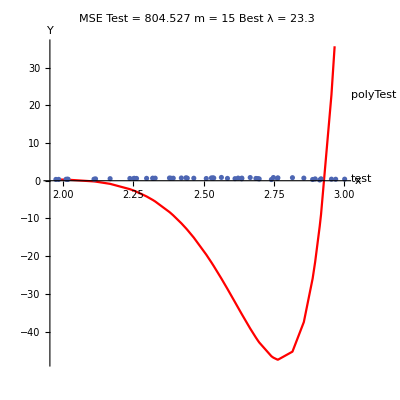

```mathematica
λ=bestLambdaRidge⟦1⟧;
m=15;
step=2;
trainParamsRidge=polyRidge[xtrain,ytrain,m,ridgePolynom,λ,step][[3]]
{polyTestRidge,mseTestRidge}=polytestRidge[xtest,ytest,trainParamsRidge,m,ridgePolynom,λ,step];
plotLabel="MSE Test = "~~ToString[mseTestRidge,TraditionalForm]~~"\n m = "~~ToString@m~~"\n Best λ = "~~ToString@λ;
ListPlot[{polyTestRidge,test},
AspectRatio->1,AxesLabel->{"x","Y"},
Joined->{True,False},PlotLabel->plotLabel,
PlotLabels->Placed[{"polyTest","test"},After],
PlotStyle->{Red,RGBColor[0.3,0.4,0.7]}]
```

Для полинома 15-ой степени мы подобрали λ=23.3, MSE=804, минимальное среди всех λ, но результат, как видно на графике выше, является очень плохим на тестовом множестве в лучшем случае.

## 3. Lasso Regression

## Lasso Polyfit

```mathematica
m=2;
λ=1;
step=1;
{polyTrainRidge,mseTrainRidge,fitParamsRidge} = polyRidge[xtrain,ytrain,m,ridgePolynom,λ,step];
```

```mathematica
fitParamsRidge
```

{θ_0→-0.302893,θ_1→0.00186625,θ_2→-2.91107×10^-9}

## Test LassoPolyfit

```mathematica
{polyTestRidge,mseTestRidge} = polytestRidge[xtest,ytest,fitParamsRidge,m,ridgePolynom,λ,step];
```

## Min (λ,15) Lasso

```mathematica
start=0;
end=30;
stepik=0.05;
m=15;
step=1;
bestFitLambdaLasso=Table[polytestRidge[xtest,ytest,polyRidge[xtrain,ytrain,m,ridgePolynom,λ,step]⟦3⟧,m,ridgePolynom,λ,step][[2]],{λ,start,end,stepik}];
```

```mathematica
posMinL=Flatten@Position[bestFitLambdaLasso,Min[bestFitLambdaLasso]];
bestLambdaLasso=Range[start,end,stepik]⟦posMinL⟧
minMSElasso=bestFitLambdaLasso⟦posMinL⟧
```

{1.25}

{76.3552}

## Visualisation Polyfit Lasso Test

{θ_0→-0.0000327031,θ_1→-4.88417×10^-9,θ_2→-1.36499×10^-8,θ_3→-2.13488×10^-9,θ_4→-8.80892×10^-9,θ_5→-4.65285×10^-9,θ_6→-1.20253×10^-8,θ_7→-5.21635×10^-9,θ_8→-1.06886×10^-8,θ_9→-3.78905×10^-9,θ_10→-1.09569×10^-8,θ_11→-6.8822×10^-9,θ_12→-6.53674×10^-9,θ_13→0.0000992471,θ_14→-1.00011×10^-8,θ_15→-9.88093×10^-6}

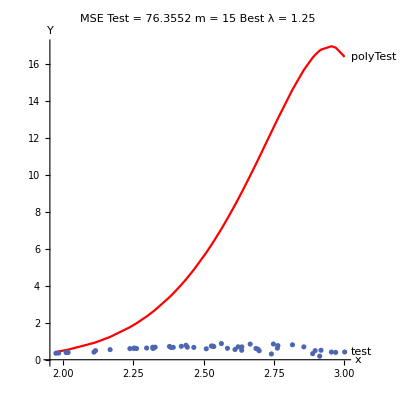

```mathematica
λ=bestLambdaLasso⟦1⟧;
m=15;
step=1;
trainParamsRidge=polyRidge[xtrain,ytrain,m,ridgePolynom,λ,step][[3]]
{polyTestRidge,mseTestLasso}=polytestRidge[xtest,ytest,trainParamsRidge,m,ridgePolynom,λ,step];
plotLabel="MSE Test = "~~ToString[mseTestLasso,TraditionalForm]~~"\n m = "~~ToString@m~~"\n Best λ = "~~ToString@λ;
ListPlot[{polyTestRidge,test},
AspectRatio->1,AxesLabel->{"x","Y"},
Joined->{True,False},PlotLabel->plotLabel,
PlotLabels->Placed[{"polyTest","test"},After],
PlotStyle->{Red,RGBColor[0.3,0.4,0.7]}]
```

В случае Lasso регуляризации для полинома 15-ой степени был подобран оптимальный коэффициент λ=1.25 с соответсвующим MSE=76, хотя видно на графике (и ожидаемо), что результаты на тестовом множестве на полиноме 15-ой степени для данной модели никак не могут быть хорошими. 
Также видно, что практически все коэффициенты подобранной модели являются шумовыми, кроме первого, хотя и он тоже близок к нулю.
Вывод: сравнивая результаты метода МНК, Ridge и Lasso, выяснили, что регуляризация Lasso помогла получить наименьшую величину ошибки среди трех рассмотренных случаев, однако данная модель все равно не может использоваться для данных точек, ведь модель переобучивается на обучающей выборки.

Результаты: степерь полинома m=15:

```mathematica
Grid[{{"Method","MSE Min","Best λ"},{"Least Squares",mseTest,"-"},{"Ridge",mseTestRidge,bestLambdaRidge⟦1⟧},{"Lasso",mseTestLasso,bestLambdaLasso⟦1⟧}},Frame->All]
```

Method | MSE Min | Best λ
Least Squares | 1.45249×10^7 | -
Ridge | 804.527 | 23.3
Lasso | 76.3552 | 1.25